```mathematica
SetDirectory["/Users/ligocki/Rupert"]
```

/Users/ligocki/Rupert

```mathematica
Needs["RupertPoly2023`"]
```

```mathematica
<<RupertPoly2023.wl
```

```mathematica
?RupertPoly2023`*
```

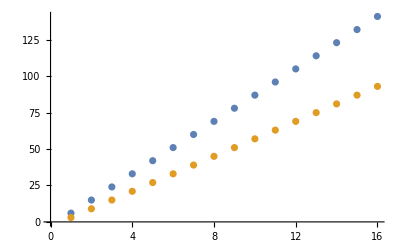

```mathematica
ListPlot[{Table[dof[3,n],{n,4,50,3}],Table[dof[3,n]-(n-1),{n,4,50,3}]}]
```

```mathematica
Collect[dof[m,n],n]
```

-1/2 m (1+m)+m n

```mathematica
Collect[Simplify[dof[m,n]-(n-1)],n]
```

-1/2 (-1+m) (2+m)+(-1+m) n

```mathematica
Collect[Simplify[dof[3,n]],n]
```

-6+3 n

```mathematica
Collect[Simplify[dof[3,n]-(n-1)],n]
```

-5+2 n

```mathematica
Table[{n,dof[3,n],dof[3,n]-(n-1)},{n,4,50,3}]//MatrixForm
```

(4 | 6 | 3
7 | 15 | 9
10 | 24 | 15
13 | 33 | 21
16 | 42 | 27
19 | 51 | 33
22 | 60 | 39
25 | 69 | 45
28 | 78 | 51
31 | 87 | 57
34 | 96 | 63
37 | 105 | 69
40 | 114 | 75
43 | 123 | 81
46 | 132 | 87
49 | 141 | 93)

```mathematica
rot[t,2,3,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[t[2,3]] | -Sin[t[2,3]] | 0
0 | Sin[t[2,3]] | Cos[t[2,3]] | 0
0 | 0 | 0 | 1)

```mathematica
rot2[x,2,3,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | √(1-x[2,3]) | -√x[2,3] | 0
0 | √x[2,3] | √(1-x[2,3]) | 0
0 | 0 | 0 | 1)

```mathematica
fullRotMat[t,1,3]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | -Sin[t[1,2]] | -Cos[t[1,2]] Sin[t[1,3]]
Cos[t[1,3]] Sin[t[1,2]] | Cos[t[1,2]] | -Sin[t[1,2]] Sin[t[1,3]]
Sin[t[1,3]] | 0 | Cos[t[1,3]])

```mathematica
fullRotMat2[t,1,3]//MatrixForm
```

(√(1-t[1,2]) √(1-t[1,3]) | -√t[1,2] | -√(1-t[1,2]) √t[1,3]
√t[1,2] √(1-t[1,3]) | √(1-t[1,2]) | -√t[1,2] √t[1,3]
√t[1,3] | 0 | √(1-t[1,3]))

```mathematica
Table[{2,n,dof[2,n],dof[2,n]-(n-1)},{n,3,5,2}]//MatrixForm
```

(2 | 3 | 3 | 1
2 | 5 | 7 | 3)

```mathematica
Table[{3,n,dof[3,n],dof[3,n]-(n-1)},{n,5,5,3}]//MatrixForm
```

(3 | 5 | 9 | 5)

```mathematica
makeCon[x,2,3,0,1]
```

{0≤x[1,2]≤1,0≤x[1,3]≤1,0≤x[2,3]≤1}

```mathematica
makeCon[t,2,3,0,2Pi]
```

{0≤t[1,2]≤2 π,0≤t[1,3]≤2 π,0≤t[2,3]≤2 π}